```mathematica
(* LOAD VARIABLES ----------------------
loads all functions and data (made in this file and evaluated previously) into memory so you don't have to run them again *)
Get[StringReplace[NotebookFileName[],".nb"->", variables.mx"]];
```

Get::noopen: Cannot open TraditionalForm`"C:\\Users\\Omar\\Dropbox\\Academic\\Projects\\9. LHV models for N Qubit Werner State\\Code\\4.Four Qubit Werner State, variables.mx".

```mathematica
(* SAVE VARIABLES ----------------
Save the variables after evaluating them initially so you don't have to re-evaluate them every time *)
DumpSave[StringReplace[NotebookFileName[],".nb"->", variables.mx"],"Global`"];
```

```mathematica
comm[x_,y_]:=x.y-y.x
```

```mathematica
acomm[x_,y_]:=x.y+y.x
```

```mathematica
pf={{{1,0},{0,1}},{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
tPauliBasis4=Table[KroneckerProduct[pf[[i]],pf[[j]],pf[[k]],pf[[l]]],{i,4},{j,4},{k,4},{l,4}];
```

```mathematica
mMixed=ConstantArray[0,{4,4,4,4}]; mMixed[[1,1,1,1]]=1;
```

```mathematica
wxyz=wyxz=wzxy=xyz=wyz=wxz=wxy=wx=wy=wz=xy=yz=xz=mMixed;
```

```mathematica
(* initiialize the three pairs *)
```

```mathematica
wxyz[[2;;4,2;;4,2;;4,2;;4]]=Table[KroneckerDelta[i,j]KroneckerDelta[k,l],{i,3},{j,3},{k,3},{l,3}];
wyxz[[2;;4,2;;4,2;;4,2;;4]]=Table[KroneckerDelta[i,k]KroneckerDelta[j,l],{i,3},{j,3},{k,3},{l,3}];
wzxy[[2;;4,2;;4,2;;4,2;;4]]=Table[KroneckerDelta[i,l]KroneckerDelta[j,k],{i,3},{j,3},{k,3},{l,3}];
```

```mathematica
wxy[[2;;4,2;;4,2;;4,1]]=LeviCivitaTensor[3];
wxz[[2;;4,2;;4,1,2;;4]]=LeviCivitaTensor[3];
wyz[[2;;4,1,2;;4,2;;4]]=LeviCivitaTensor[3];
xyz[[1,2;;4,2;;4,2;;4]]=LeviCivitaTensor[3];
```

```mathematica
wx[[2;;4,2;;4,1,1]]=IdentityMatrix[3];
wy[[2;;4,1,2;;4,1]]=IdentityMatrix[3];
wz[[2;;4,1,1,2;;4]]=IdentityMatrix[3];
xy[[1,2;;4,2;;4,1]]=IdentityMatrix[3];
xz[[1,2;;4,1,2;;4]]=IdentityMatrix[3];
yz[[1,1,2;;4,2;;4]]=IdentityMatrix[3];
```

```mathematica
Clear[awx,awy,awz,axy,axz,ayz,bwxy,bwxz,bwyz,bxyz,cwxyz,cwyxz,cwzxy];
coeff={awx,awy,awz,axy,axz,ayz,bwxy,bwxz,bwyz,bxyz,cwxyz,cwyxz,cwzxy};
```

```mathematica
BlochTensor4=Simplify[mMixed(1-Total[coeff])+coeff.{wx,wy,wz,xy,xz,yz,wxy,wxz,wyz,xyz,wxyz,wyxz,wzxy}]
```

((1 | 0 | 0 | 0
0 | ayz | 0 | 0
0 | 0 | ayz | 0
0 | 0 | 0 | ayz) | (0 | axz | 0 | 0
axy | 0 | 0 | 0
0 | 0 | 0 | bxyz
0 | 0 | -bxyz | 0) | (0 | 0 | axz | 0
0 | 0 | 0 | -bxyz
axy | 0 | 0 | 0
0 | bxyz | 0 | 0) | (0 | 0 | 0 | axz
0 | 0 | bxyz | 0
0 | -bxyz | 0 | 0
axy | 0 | 0 | 0)
(0 | awz | 0 | 0
awy | 0 | 0 | 0
0 | 0 | 0 | bwyz
0 | 0 | -bwyz | 0) | (awx | 0 | 0 | 0
0 | cwxyz+cwyxz+cwzxy | 0 | 0
0 | 0 | cwxyz | 0
0 | 0 | 0 | cwxyz) | (0 | 0 | 0 | bwxz
0 | 0 | cwyxz | 0
0 | cwzxy | 0 | 0
bwxy | 0 | 0 | 0) | (0 | 0 | -bwxz | 0
0 | 0 | 0 | cwyxz
-bwxy | 0 | 0 | 0
0 | cwzxy | 0 | 0)
(0 | 0 | awz | 0
0 | 0 | 0 | -bwyz
awy | 0 | 0 | 0
0 | bwyz | 0 | 0) | (0 | 0 | 0 | -bwxz
0 | 0 | cwzxy | 0
0 | cwyxz | 0 | 0
-bwxy | 0 | 0 | 0) | (awx | 0 | 0 | 0
0 | cwxyz | 0 | 0
0 | 0 | cwxyz+cwyxz+cwzxy | 0
0 | 0 | 0 | cwxyz) | (0 | bwxz | 0 | 0
bwxy | 0 | 0 | 0
0 | 0 | 0 | cwyxz
0 | 0 | cwzxy | 0)
(0 | 0 | 0 | awz
0 | 0 | bwyz | 0
0 | -bwyz | 0 | 0
awy | 0 | 0 | 0) | (0 | 0 | bwxz | 0
0 | 0 | 0 | cwzxy
bwxy | 0 | 0 | 0
0 | cwyxz | 0 | 0) | (0 | -bwxz | 0 | 0
-bwxy | 0 | 0 | 0
0 | 0 | 0 | cwzxy
0 | 0 | cwyxz | 0) | (awx | 0 | 0 | 0
0 | cwxyz | 0 | 0
0 | 0 | cwxyz | 0
0 | 0 | 0 | cwxyz+cwyxz+cwzxy))

```mathematica
rho4=Total[BlochTensor4*tPauliBasis4,4]/16;
```

```mathematica
rhoSolely4=rho4/.{awx-> 0,awy-> 0,awz-> 0,axy-> 0,axz-> 0,ayz-> 0,bwxy-> 0,bwxz-> 0,bwyz-> 0,bxyz-> 0,cwxyz-> a,cwyxz-> b,cwzxy-> c};
rhoSolely3=rho4/.{awx-> 0,awy-> 0,awz-> 0,axy-> 0,axz-> 0,ayz-> 0,cwxyz-> 0,cwyxz-> 0,cwzxy-> 0,bwxy-> a,bwxz-> -b,bwyz-> c,bxyz-> -d};
rhoSolely2=rho4/.{bwxy-> 0,bwxz-> 0,bwyz-> 0,bxyz-> 0,cwxyz-> 0,cwyxz-> 0,cwzxy-> 0,awx-> a,awy-> b,awz-> c,axy-> d,axz-> e,ayz-> f};
```

```mathematica
16DeleteDuplicates[Eigenvalues[rhoSolely4]]
```

{a-3 b-3 c+1,-3 a+b-3 c+1,-3 a-3 b+c+1,a+b+c+1,-4 √(a^2-a b-a c+b^2-b c+c^2)+5 a+5 b+5 c+1,4 √(a^2-a b-a c+b^2-b c+c^2)+5 a+5 b+5 c+1}

```mathematica
evSole3=Simplify[16DeleteDuplicates[Eigenvalues[rhoSolely3]]]
```

{1,1-2 √3 √((a+b+c+d)^2),2 √3 √((a+b+c+d)^2)+1,1-2 √(3 a^2-2 a (b+c+d)+3 b^2-2 b (c+d)+3 c^2-2 c d+3 d^2),2 √(3 a^2-2 a (b+c+d)+3 b^2-2 b (c+d)+3 c^2-2 c d+3 d^2)+1}

```mathematica
(* equal implies |a|≤ 1/(8√3) *)
evSole3/.{b->a,c->a,d->a}
```

{1,1-8 √3 √(a^2),8 √3 √(a^2)+1,1,1}

```mathematica
(* almost like normal modes *)
```

```mathematica
(* alternating implies |a|≤ 1/8 *)
evSole3/.{b->-a,c->a,d->-a}
```

{1,1,1,1-8 √(a^2),8 √(a^2)+1}

```mathematica
16DeleteDuplicates[Eigenvalues[rhoSolely2]]
```

{a+b+c+d+e+f+1,-a-b-c-d-e-f-2 √(a^2-b a-c a-d a-e a+2 f a+b^2+c^2+d^2+e^2+f^2-b c-b d+2 c d+2 b e-c e-d e-b f-c f-d f-e f)+1,-a-b-c-d-e-f+2 √(a^2-b a-c a-d a-e a+2 f a+b^2+c^2+d^2+e^2+f^2-b c-b d+2 c d+2 b e-c e-d e-b f-c f-d f-e f)+1,Root[3 a^3-3 b a^2-3 c a^2-3 d a^2-3 e a^2-7 f a^2+5 a^2-3 b^2 a-3 c^2 a-3 d^2 a-3 e^2 a-7 f^2 a-2 b a+14 b c a-2 c a-18 b d a+10 c d a-2 d a+10 b e a-18 c e a+14 d e a-2 e a+10 b f a+10 c f a+10 d f a+10 e f a-6 f a+a+3 b^3+3 c^3+3 d^3+3 e^3+3 f^3+#1^3+5 b^2-3 b c^2+5 c^2-3 b d^2-7 c d^2+5 d^2-7 b e^2-3 c e^2-3 d e^2+5 e^2-3 b f^2-3 c f^2-3 d f^2-3 e f^2+5 f^2+(a+b+c+d+e+f-3) #1^2+b-3 b^2 c-2 b c+c-3 b^2 d-7 c^2 d-2 b d+10 b c d-6 c d+d-7 b^2 e-3 c^2 e-3 d^2 e-6 b e+10 b c e-2 c e+10 b d e+10 c d e-2 d e+e-3 b^2 f-3 c^2 f-3 d^2 f-3 e^2 f-2 b f-18 b c f-2 c f+14 b d f+10 c d f-2 d f+10 b e f+14 c e f-18 d e f-2 e f+f+(-5 a^2+2 b a+2 c a+2 d a+2 e a+6 f a-2 a-5 b^2-5 c^2-5 d^2-5 e^2-5 f^2-2 b+2 b c-2 c+2 b d+6 c d-2 d+6 b e+2 c e+2 d e-2 e+2 b f+2 c f+2 d f+2 e f-2 f+3) #1-1&,1],Root[3 a^3-3 b a^2-3 c a^2-3 d a^2-3 e a^2-7 f a^2+5 a^2-3 b^2 a-3 c^2 a-3 d^2 a-3 e^2 a-7 f^2 a-2 b a+14 b c a-2 c a-18 b d a+10 c d a-2 d a+10 b e a-18 c e a+14 d e a-2 e a+10 b f a+10 c f a+10 d f a+10 e f a-6 f a+a+3 b^3+3 c^3+3 d^3+3 e^3+3 f^3+#1^3+5 b^2-3 b c^2+5 c^2-3 b d^2-7 c d^2+5 d^2-7 b e^2-3 c e^2-3 d e^2+5 e^2-3 b f^2-3 c f^2-3 d f^2-3 e f^2+5 f^2+(a+b+c+d+e+f-3) #1^2+b-3 b^2 c-2 b c+c-3 b^2 d-7 c^2 d-2 b d+10 b c d-6 c d+d-7 b^2 e-3 c^2 e-3 d^2 e-6 b e+10 b c e-2 c e+10 b d e+10 c d e-2 d e+e-3 b^2 f-3 c^2 f-3 d^2 f-3 e^2 f-2 b f-18 b c f-2 c f+14 b d f+10 c d f-2 d f+10 b e f+14 c e f-18 d e f-2 e f+f+(-5 a^2+2 b a+2 c a+2 d a+2 e a+6 f a-2 a-5 b^2-5 c^2-5 d^2-5 e^2-5 f^2-2 b+2 b c-2 c+2 b d+6 c d-2 d+6 b e+2 c e+2 d e-2 e+2 b f+2 c f+2 d f+2 e f-2 f+3) #1-1&,2],Root[3 a^3-3 b a^2-3 c a^2-3 d a^2-3 e a^2-7 f a^2+5 a^2-3 b^2 a-3 c^2 a-3 d^2 a-3 e^2 a-7 f^2 a-2 b a+14 b c a-2 c a-18 b d a+10 c d a-2 d a+10 b e a-18 c e a+14 d e a-2 e a+10 b f a+10 c f a+10 d f a+10 e f a-6 f a+a+3 b^3+3 c^3+3 d^3+3 e^3+3 f^3+#1^3+5 b^2-3 b c^2+5 c^2-3 b d^2-7 c d^2+5 d^2-7 b e^2-3 c e^2-3 d e^2+5 e^2-3 b f^2-3 c f^2-3 d f^2-3 e f^2+5 f^2+(a+b+c+d+e+f-3) #1^2+b-3 b^2 c-2 b c+c-3 b^2 d-7 c^2 d-2 b d+10 b c d-6 c d+d-7 b^2 e-3 c^2 e-3 d^2 e-6 b e+10 b c e-2 c e+10 b d e+10 c d e-2 d e+e-3 b^2 f-3 c^2 f-3 d^2 f-3 e^2 f-2 b f-18 b c f-2 c f+14 b d f+10 c d f-2 d f+10 b e f+14 c e f-18 d e f-2 e f+f+(-5 a^2+2 b a+2 c a+2 d a+2 e a+6 f a-2 a-5 b^2-5 c^2-5 d^2-5 e^2-5 f^2-2 b+2 b c-2 c+2 b d+6 c d-2 d+6 b e+2 c e+2 d e-2 e+2 b f+2 c f+2 d f+2 e f-2 f+3) #1-1&,3]}

```mathematica
(* like each pair is entangled, but the two entanglements are then entangled *)
```

```mathematica
(* ----- PURITY --- *)
purSole4=Simplify[Tr[rhoSolely4.rhoSolely4]]
```

1/16 (9 a^2+6 a (b+c)+9 b^2+6 b c+9 c^2+1)

```mathematica
purSole3=Simplify[Tr[rhoSolely3.rhoSolely3]]
```

1/16 (6 a^2+6 b^2+6 c^2+6 d^2+1)

```mathematica
purSole4/.{a-> 1/5,b->1/5,c->1/5}
```

7/40

```mathematica
purSole4/.{a-> 2/5,b->-1/10,c->-1/10}
```

11/80

```mathematica
(* -------- PLOTS --------- *)
```

```mathematica
llim=-1/5;ulim=2/5;op=1;ppts=10;
PlotPSurface4[viewvector_:viewVec,purflag_:False]:=Module[{flata,flatb,flatc,back,point,purity},
flata=ContourPlot3D[a-3 b-3 c+1==0,{a,llim,ulim},{b,llim,ulim},{c,llim,ulim},PlotPoints->ppts, MeshStyle->Opacity[op],ContourStyle->Directive[Opacity[op]],RegionFunction-> Function[{a,b,c },-3 a+b-3 c+1≥0&&-3 a-3 b+c+1≥0&&-4 √(a^2-a b-a c+b^2-b c+c^2)+5 a+5 b+5 c+1≥0 ]];
flatb=ContourPlot3D[-3a+ b-3 c+1==0,{a,llim,ulim},{b,llim,ulim},{c,llim,ulim},PlotPoints->ppts, MeshStyle->Opacity[op],ContourStyle->Directive[Opacity[op]],RegionFunction-> Function[{a,b,c },a-3b-3 c+1≥0&&-3 a-3 b+c+1≥0&&-4 √(a^2-a b-a c+b^2-b c+c^2)+5 a+5 b+5 c+1≥0 ]];
flatc=ContourPlot3D[-3a-3 b+c+1==0,{a,llim,ulim},{b,llim,ulim},{c,llim,ulim},PlotPoints->ppts, MeshStyle->Opacity[op],ContourStyle->Directive[Opacity[op]],RegionFunction-> Function[{a,b,c },a-3 b-3 c+1≥0&&-3a+ b-3 c+1≥0&&-4 √(a^2-a b-a c+b^2-b c+c^2)+5 a+5 b+5 c+1≥0 ]];
back=ContourPlot3D[-4 √(a^2-a b-a c+b^2-b c+c^2)+5 a+5 b+5 c+1  ==0,{a,llim,ulim},{b,llim,ulim},{c,llim,ulim},PlotPoints->ppts, MeshStyle->Opacity[op],ContourStyle->Directive[Opacity[op]],RegionFunction-> Function[{a,b,c },a-3 b-3 c+1≥0&&-3 a+b-3 c+1≥0&&-3 a-3 b+c+1≥0 ]];
point=Graphics3D[{Black,Sphere[0.41{1,1,1},0.008]}];
purity=If[purflag,ContourPlot3D[1/16 (9 a^2+9 b^2+9 c^2+6 a b+6a c+6 b c+1)==7/40,{a,llim,ulim},{b,llim,ulim},{c,llim,ulim},PlotPoints->ppts, MeshStyle->Opacity[op/2],ContourStyle->Directive[Red,Opacity[op/2]]],{}];
Show[flata,flatb,flatc,back,purity,point,ViewPoint->viewvector,TicksStyle->Directive[FontOpacity->0,FontSize->0]]
]
```

```mathematica
(* to extract current viewing vector ... initialize it to defailt *)
viewVec=Options[Graphics3D,ViewPoint][[1,2]];
```

```mathematica
PlotPSurface4[Dynamic[viewVec],True]
```

-Graphics3D-

```mathematica
viewVec
```

{-1.16613,-3.17153,-0.177501}

```mathematica
N4Space1=PlotPSurface4[{2.7,1.9,0.72}]
```

-Graphics3D-

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>  "\Lyx v1\N4Space1.pdf",N4Space1];
```

```mathematica
N4Space2=PlotPSurface4[{-1.2,-3.2,-0.18}]
```

-Graphics3D-

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>  "\Lyx v1\N4Space2.pdf",N4Space2];
```

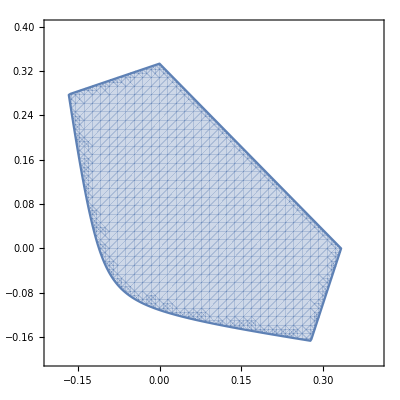

```mathematica
(* plane cross section *)
c=0;llim=-.2;ulim=.4;RegionPlot[a-3 b-3 c+1≥0&&-3 a+b-3 c+1≥0&&-3 a-3 b+c+1≥0&&-4 √(a^2-a b-a c+b^2-b c+c^2)+5 a+5 b+5 c+1≥0,{a,llim,lim},{b,llim,lim}, PlotPoints->40]
```